```mathematica
Quit
```

```mathematica
<<"~/Github/1plus1d/OneFlavour.m"
```

```mathematica
mQ=4.23;n1=n2=n3=n4=0;
```

```mathematica
(*SetOptions[NIntegrate,MaxRecursion->200,AccuracyGoal->15(*,WorkingPrecision->30*)];*)
```

```mathematica
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=(g^2 Nc)/(2 π)*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
gglo=1;Nc=(β^2 2π)/g^2;(*ℂ denotes the interchange of final states.*)
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
Mn[n_][vals_]:=vals[[n+1]];

ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-Sqrt[s] Sqrt[(M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s])/(M3^2-M4^2+s+Sqrt[s] Sqrt[(M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s]);
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-Sqrt[s] Sqrt[(M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s])/(M3^2-M4^2+s+Sqrt[s] Sqrt[(M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s]);
```

```mathematica
If[$OperatingSystem=="Windows",{dirglo="D:/Documents/2-d-data";},{dirglo="~/Documents/2-d-data";}];
```

```mathematica
ℐ1[ω1_,ω2_,opt:OptionsPattern[]][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2 (NIntegrate[(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,{z,0,1},{x,0,1-10^-10},{y,0,1},Evaluate[FilterRules[{opt},Options[NIntegrate]]]](*+(ω2 NIntegrate[(ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2])/(((ω1-(1-x) ω2) ((ω1-(1-x) ω2)/ω1-1))/ω1),{x,0,1}])/ω1*));
ℐ2[ω1_,ω2_,opt:OptionsPattern[]][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2 (NIntegrate[(ω1 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] (ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2]-ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2]-(y-x/ω1) (ϕ4[((-1+x/ω1) ω1+ω2)/ω2] ϕ2'[x/ω1]+(ω1 ϕ2[x/ω1] ϕ4'[((-1+x/ω1) ω1+ω2)/ω2])/ω2))))/(y ω1-x)^2,{z,0,1},{x,10^-10,1},{y,0,1},Evaluate[FilterRules[{opt},Options[NIntegrate]]]](*+NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2])/((x (x/ω1-1))/ω1),{x,0,1}]/ω1*));
```

```mathematica
EXPR[ω1_,ω2_,opt:OptionsPattern[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]}]][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ1[1/ω1,(1-ω1+ω2)/ω1,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I1Option]]][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2),(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I2Option]]][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ1[ω1,ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I1Option]]][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ2[ω1/ω2,1/ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I2Option]]][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ1[ω1/ω2,1/ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I1Option]]][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I2Option]]][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I1Option]]][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2),(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I2Option]]][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]+Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I3Option]]][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I3Option]]][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I3Option]]][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I3Option]]][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I3Option]]][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[(1-ω1+ω2)/ω2,1/ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I3Option]]][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2),(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I3Option]]][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2),(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[I3Option]]][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]];
```

```mathematica
EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]=If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m1,M2,M1,M3,M4]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m1,M4,M3,M1,M2]+ℐ1[1/ω1,(1-ω1+ω2)/ω1,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I1Option]]][ϕ4,ϕ3,ϕ2,ϕ1][m1,M4,M3,M2,M1]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2),(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I2Option]]][ϕ4,ϕ3,ϕ1,ϕ2][m1,M4,M3,M1,M2],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m1,M3,M4,M2,M1]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m1,M1,M2,M4,M3]+ℐ1[ω1,ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I1Option]]][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I2Option]]][ϕ1,ϕ2,ϕ4,ϕ3][m1,M1,M2,M4,M3]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m1,M4,M3,M2,M1]+ℐ1[ω1/ω2,1/ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I1Option]]][ϕ1,ϕ2,ϕ4,ϕ3][m1,M1,M2,M4,M3]+ℐ2[ω1,ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I2Option]]][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m1,M2,M1,M4,M3]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m1,M3,M4,M1,M2]+ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I1Option]]][ϕ3,ϕ4,ϕ2,ϕ1][m1,M3,M4,M2,M1]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2),(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I2Option]]][ϕ3,ϕ4,ϕ1,ϕ2][m1,M3,M4,M1,M2]]+Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I3Option]]][ϕ4,ϕ3,ϕ2,ϕ1][m1,M4,M3,M2,M1]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I3Option]]][ϕ3,ϕ4,ϕ2,ϕ1][m1,M3,M4,M2,M1],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I3Option]]][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I3Option]]][ϕ2,ϕ1,ϕ3,ϕ4][m1,M2,M1,M3,M4],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I3Option]]][ϕ1,ϕ2,ϕ4,ϕ3][m1,M1,M2,M4,M3]+ℐ3[(1-ω1+ω2)/ω2,1/ω2,(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I3Option]]][ϕ2,ϕ1,ϕ4,ϕ3][m1,M2,M1,M4,M3],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2),(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I3Option]]][ϕ4,ϕ3,ϕ1,ϕ2][m1,M4,M3,M1,M2]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2),(Evaluate[If[ListQ[#1],FilterRules[#1,Options[NIntegrate]],{}]]&)[OptionValue[{I1Option->OptionsPattern[],I2Option->OptionsPattern[],I3Option->OptionsPattern[]},{},I3Option]]][ϕ3,ϕ4,ϕ1,ϕ2][m1,M3,M4,M1,M2]]
```

```mathematica
m1=mQ;m2=mQ;λ=10^-6;g=gglo;dir=dirglo;Nx=OptionValue[MatrixSize];
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
(*If[FileNames[filenameacc,dir,Infinity]=={},*)(*If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"BSW method"->True,"Brute force integration"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];*)
filename=filenameacc;Determine=accDetermineϕ;
If[FileNames[filename,dir,Infinity]=={},
,
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[Global`x_],(*Boole[0<Global`x<1]*)ϕxB};
}
];
(*Set@@{ΦB[x_?NumberQ],If[0<x<1,ΦBi[x],Table[0,{n,Length@ϕxB}]]};*)
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,M2,M3,M4}=Mn[#][ValsB]&/@{n1,n2,n3,n4};
(*Print[ϕ1[x]];*)
Mseq=Sequence[M1,M2,M3,M4];Si=If[n1+n2>=n3+n4,M1+M2,M3+M4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
```

Wavefunction build complete.

M1=9.10387  M2=9.10387  M3=9.10387  M4=9.10387

```mathematica
Clear[ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
Clear@ΦB
```

```mathematica
ϕ1[x]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 0≤x≤1.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕn[0][ΦB][x].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x>1||x<0.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

$Aborted

```mathematica
?ϕ1
```

Global`ϕ1

ϕ1[x_]:=Piecewise[{{ϕn[0][ΦB][x],0<x<1},{(ϕn[0][ΦB][z])/((x-z)^2 ((m1^2-1)/x+(m2^2-1)/(1-x)-M1^2)),x>1||x<0}},0]

```mathematica
ϕn[0][ΦB][0]
```

0.

```mathematica
ϕ1[x_?NumberQ]:=Piecewise[{{ϕn[0][ΦB][x],0<x<1},{((ϕn[0][ΦB][z])/(x-z)^2)/((m1^2-1)/x+(m2^2-1)/(1-x)-M1^2),x>1||x<0}},0]
```

```mathematica
ϕ1[x_]:=Piecewise[{{ϕn[0][ΦB][x],0<x<1},{((ϕn[0][ΦB][z])/(x-z)^2)/((m1^2-1)/x+(m2^2-1)/(1-x)-M1^2),x>1||x<0}},0]
```

```mathematica
D[(ϕ[z]/(x-z)^2)/((m^2-1)/x+(m^2-1)/(1-x)-M^2),x]
```

-(2 ϕ[z])/((-M^2+(-1+m^2)/(1-x)+(-1+m^2)/x) (x-z)^3)-(((-1+m^2)/(1-x)^2-(-1+m^2)/x^2) ϕ[z])/((-M^2+(-1+m^2)/(1-x)+(-1+m^2)/x)^2 (x-z)^2)

```mathematica
ϕ2=ϕ3=ϕ4=ϕ1;
```

```mathematica
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]//AbsoluteTiming
```

{4.93825,6.35752}

```mathematica
1/((y-1) 0.3933742034554902+(1-x) 0.3933742034554902)^2 0.3933742034554902 0.3933742034554902 (ϕ1[(x 0.3933742034554902)/(1+0.3933742034554902-0.3933742034554902)] ϕ1[x] (ϕ1[y] ϕ1[y 0.3933742034554902]-ϕ1[(0.3933742034554902-(1-x) 0.3933742034554902)/0.3933742034554902] ϕ1[0.3933742034554902-(1-x) 0.3933742034554902]-(y-(0.3933742034554902-(1-x) 0.3933742034554902)/0.3933742034554902) (ϕ1[0.3933742034554902-(1-x) 0.3933742034554902] ϕ1'[(0.3933742034554902-(1-x) 0.3933742034554902)/0.3933742034554902]+0.3933742034554902 ϕ1[(0.3933742034554902-(1-x) 0.3933742034554902)/0.3933742034554902] ϕ1'[0.3933742034554902-(1-x) 0.3933742034554902])))/.{x->0.1,y->0.9}
```

0.00234701 (0.0897325-0.8 (0.0287039 ϕ1'[0.0393374]+0.0205854 ϕ1'[0.1]))

```mathematica
ϕ1'[0.03933742034554899]
```

ϕ1'[0.0393374]

```mathematica
ϕ1'[0.3]
```

ϕ1'[0.3]

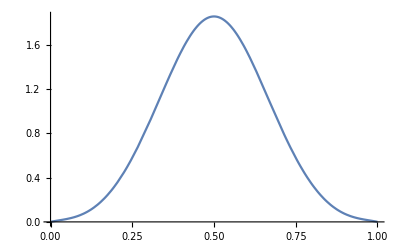

```mathematica
Plot[ϕ1[x],{x,-1,1},PlotRange->All]
```

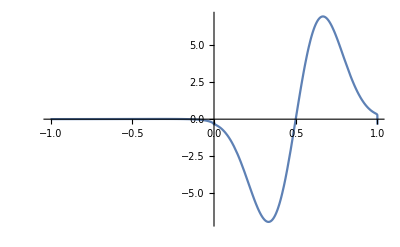

```mathematica
Plot[NIntegrate[ϕ1'[x],{z,0,1}],{x,-1,1},PlotRange->All]
```

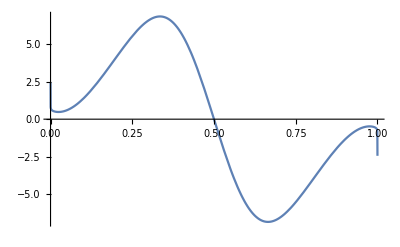

```mathematica
Plot[ϕn[0][ΦB]'[x],{x,0,1}]
```

```mathematica
Block[{Ssqur=Si+2.+10^-3},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];]
```

```mathematica
ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]//AbsoluteTiming
```

{1.47056,-25.5241}

```mathematica
ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]//AbsoluteTiming
```

{0.507943,6.25891}

```mathematica
ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]//AbsoluteTiming
```

{6.70444,-25.5237}

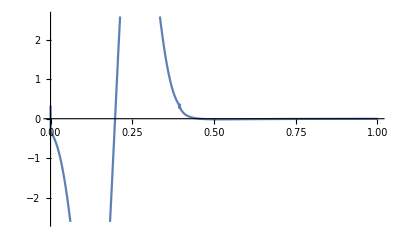

```mathematica
Plot[NIntegrate[ϕ1'[((-1+x/0.3948427167136203) 0.3948427167136203+0.3948427167136203)/0.3948427167136203],{z,0,1}],{x,0,1}]
```

```mathematica
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]
```

-25.5237

```mathematica
Block[{ω1,ω2,ϕ1,ϕ2,ϕ3,ϕ4},(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2/.{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1}]
```

1/(ω1^2 ((-1+y)/ω1+((1-x) (1-ω1+ω2))/ω1)^2)4.02649 (1-ω1+ω2) Boole[0<x<1] Boole[0<(x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))<1] (0.343526 (1-x)^1.06207 x^0.937928+0.346584 (1-x)^0.937928 x^1.06207-0.841569 Sin[π x]+0.000042429 Sin[2 π x]+0.230083 Sin[3 π x]+9.86781×10^-6 Sin[4 π x]-0.0263305 Sin[5 π x]+4.64373×10^-6 Sin[6 π x]+0.000548951 Sin[7 π x]+3.68061×10^-6 Sin[8 π x]) (0.346584 ((x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1)))^1.06207 (1-(x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1)))^0.937928+0.343526 ((x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1)))^0.937928 (1-(x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1)))^1.06207-0.841569 Sin[(π x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))]+0.000042429 Sin[(2 π x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))]+0.230083 Sin[(3 π x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))]+9.86781×10^-6 Sin[(4 π x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))]-0.0263305 Sin[(5 π x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))]+4.64373×10^-6 Sin[(6 π x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))]+0.000548951 Sin[(7 π x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))]+3.68061×10^-6 Sin[(8 π x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))]) (4.02649 Boole[0<y<1] Boole[0<y/ω1<1] (0.343526 (1-y)^1.06207 y^0.937928+0.346584 (1-y)^0.937928 y^1.06207-0.841569 Sin[π y]+0.000042429 Sin[2 π y]+0.230083 Sin[3 π y]+9.86781×10^-6 Sin[4 π y]-0.0263305 Sin[5 π y]+4.64373×10^-6 Sin[6 π y]+0.000548951 Sin[7 π y]+3.68061×10^-6 Sin[8 π y]) (0.343526 (1-y/ω1)^1.06207 (y/ω1)^0.937928+0.346584 (1-y/ω1)^0.937928 (y/ω1)^1.06207-0.841569 Sin[(π y)/ω1]+0.000042429 Sin[(2 π y)/ω1]+0.230083 Sin[(3 π y)/ω1]+9.86781×10^-6 Sin[(4 π y)/ω1]-0.0263305 Sin[(5 π y)/ω1]+4.64373×10^-6 Sin[(6 π y)/ω1]+0.000548951 Sin[(7 π y)/ω1]+3.68061×10^-6 Sin[(8 π y)/ω1])-(y-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)) (2.00661 Boole[0<1/ω1-((1-x) (1-ω1+ω2))/ω1<1] (0.346584 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^1.06207 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^0.937928+0.343526 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^0.937928 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^1.06207-0.841569 Sin[π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000042429 Sin[2 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.230083 Sin[3 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+9.86781×10^-6 Sin[4 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-0.0263305 Sin[5 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+4.64373×10^-6 Sin[6 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000548951 Sin[7 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+3.68061×10^-6 Sin[8 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]) (2.00661 Boole[0<ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)<1] (-(0.325071 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^1.06207)/(1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.062072-0.364849 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.937928 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.062072+0.368098 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.062072 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.937928+(0.322203 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^1.06207)/(ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.062072-2.64387 Cos[π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000266589 Cos[2 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+2.16848 Cos[3 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000124003 Cos[4 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-0.413599 Cos[5 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.0000875323 Cos[6 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.0120721 Cos[7 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.0000925039 Cos[8 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)])+2.00661 (Piecewise[{{0, ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)<0||0<ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)<1||ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)>1}, {Indeterminate, True}}]) (0.346584 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^1.06207 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.937928+0.343526 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.937928 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^1.06207-0.841569 Sin[π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000042429 Sin[2 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.230083 Sin[3 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+9.86781×10^-6 Sin[4 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-0.0263305 Sin[5 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+4.64373×10^-6 Sin[6 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000548951 Sin[7 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+3.68061×10^-6 Sin[8 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]))+1/ω1 2.00661 Boole[0<ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)<1] (2.00661 Boole[0<1/ω1-((1-x) (1-ω1+ω2))/ω1<1] (-(0.325071 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^1.06207)/(1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^0.062072-0.364849 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^0.937928 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^0.062072+0.368098 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^0.062072 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^0.937928+(0.322203 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^1.06207)/(1/ω1-((1-x) (1-ω1+ω2))/ω1)^0.062072-2.64387 Cos[π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000266589 Cos[2 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+2.16848 Cos[3 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000124003 Cos[4 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-0.413599 Cos[5 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.0000875323 Cos[6 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.0120721 Cos[7 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.0000925039 Cos[8 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)])+2.00661 (Piecewise[{{0, 1/ω1-((1-x) (1-ω1+ω2))/ω1<0||0<1/ω1-((1-x) (1-ω1+ω2))/ω1<1||1/ω1-((1-x) (1-ω1+ω2))/ω1>1}, {Indeterminate, True}}]) (0.346584 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^1.06207 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^0.937928+0.343526 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^0.937928 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^1.06207-0.841569 Sin[π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000042429 Sin[2 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.230083 Sin[3 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+9.86781×10^-6 Sin[4 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-0.0263305 Sin[5 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+4.64373×10^-6 Sin[6 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000548951 Sin[7 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+3.68061×10^-6 Sin[8 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)])) (0.346584 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^1.06207 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.937928+0.343526 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.937928 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^1.06207-0.841569 Sin[π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000042429 Sin[2 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.230083 Sin[3 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+9.86781×10^-6 Sin[4 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-0.0263305 Sin[5 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+4.64373×10^-6 Sin[6 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000548951 Sin[7 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+3.68061×10^-6 Sin[8 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]))-4.02649 Boole[0<1/ω1-((1-x) (1-ω1+ω2))/ω1<1] Boole[0<ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)<1] (0.346584 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^1.06207 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^0.937928+0.343526 (1/ω1-((1-x) (1-ω1+ω2))/ω1)^0.937928 (1-1/ω1+((1-x) (1-ω1+ω2))/ω1)^1.06207-0.841569 Sin[π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000042429 Sin[2 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.230083 Sin[3 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+9.86781×10^-6 Sin[4 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-0.0263305 Sin[5 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+4.64373×10^-6 Sin[6 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000548951 Sin[7 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+3.68061×10^-6 Sin[8 π (1/ω1-((1-x) (1-ω1+ω2))/ω1)]) (0.346584 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^1.06207 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.937928+0.343526 (ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^0.937928 (1-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1))^1.06207-0.841569 Sin[π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000042429 Sin[2 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.230083 Sin[3 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+9.86781×10^-6 Sin[4 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-0.0263305 Sin[5 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+4.64373×10^-6 Sin[6 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+0.000548951 Sin[7 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]+3.68061×10^-6 Sin[8 π ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]))

```mathematica
%//Simplify
```

((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/ω2] ϕ4[x] (ϕ2[y] ϕ3[y/ω1]-ϕ2[x+ω1-x ω1-ω2+x ω2] ϕ3[(x+ω1-x ω1-ω2+x ω2)/ω1]-((y-ω1+x (-1+ω1-ω2)+ω2) (ω1 ϕ3[(x+ω1-x ω1-ω2+x ω2)/ω1] ϕ2'[x+ω1-x ω1-ω2+x ω2]+ϕ2[x+ω1-x ω1-ω2+x ω2] ϕ3'[(x+ω1-x ω1-ω2+x ω2)/ω1]))/ω1))/(y-ω1+x (-1+ω1-ω2)+ω2)^2

```mathematica
Table[NIntegrate[ϕ1[z]/(x-z)^2,{z,0,1}]-((m1^2-1)/x+(m2^2-1)/(1-x)-M1^2)ϕ1[x],{x,{-0.1(*,-1.1001*),-2}}]
```

{1.33227×10^-15,-1.38778×10^-17}

```mathematica
ϕ1'[0.]
```

ϕ1'[0.]

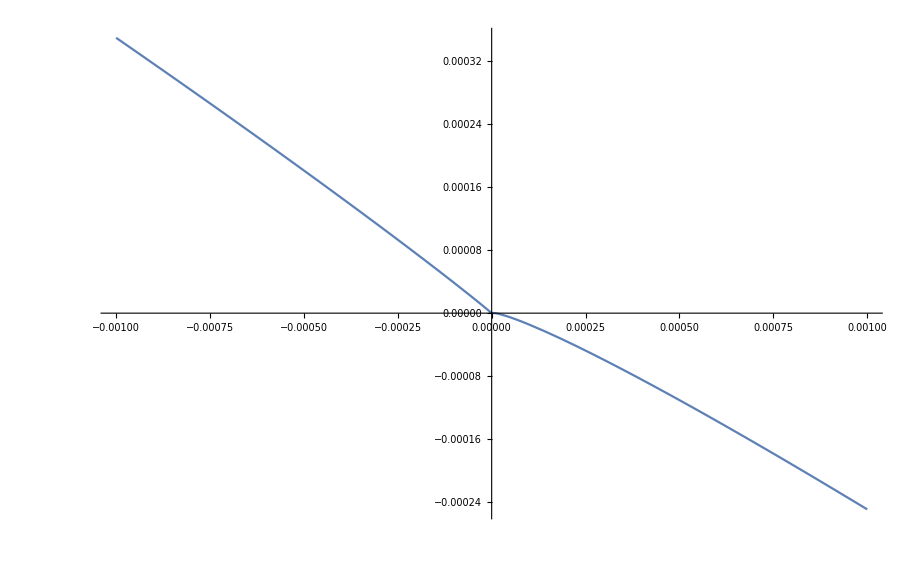

```mathematica
Plot[Re@ϕ1[x],{x,-0.001,0.001},PlotRange->All]
```

```mathematica
Block[{Ssqur=Si+2.+10^-3},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];NIntegrate[((1-ω1+ω2) ϕ1[x] ϕ4[(x (1-ω1+ω2))/(ω1 (1-1/ω1+(1-ω1+ω2)/ω1))] (ϕ2[y/ω1] ϕ3[y]-ϕ2[1/ω1-((1-x) (1-ω1+ω2))/ω1] ϕ3[ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)]-(y-ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)) ((ϕ3[ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)] ϕ2'[1/ω1-((1-x) (1-ω1+ω2))/ω1])/ω1+ϕ2[1/ω1-((1-x) (1-ω1+ω2))/ω1] ϕ3'[ω1 (1/ω1-((1-x) (1-ω1+ω2))/ω1)])))/(ω1^2 ((-1+y)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,0,1},{z,0,1},MaxRecursion->50]]//AbsoluteTiming
```

{15.6531,-1.76384+2.62686×10^-38 ⅈ}

```mathematica
ϕ2'[1]
```

Power::infy: Infinite expression 1/0^0.062072 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/ω2] ϕ4[x] (ϕ2[y] ϕ3[y/ω1]-ϕ2[x+ω1-x ω1-ω2+x ω2] ϕ3[(x+ω1-x ω1-ω2+x ω2)/ω1]-((y-ω1+x (-1+ω1-ω2)+ω2) (ω1 ϕ3[(x+ω1-x ω1-ω2+x ω2)/ω1] ϕ2'[x+ω1-x ω1-ω2+x ω2]+ϕ2[x+ω1-x ω1-ω2+x ω2] ϕ3'[(x+ω1-x ω1-ω2+x ω2)/ω1]))/ω1))/(y-ω1+x (-1+ω1-ω2)+ω2)^2,x->1]
```

0.

```mathematica
ϕ3[0.9/ω1]
```

0.+0. ⅈ

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
NIntegrate[(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,{x,0,1-10^-10},{y,0,1}]]
```

-26.2845

```mathematica
-4 g^2 (NIntegrate[(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,{x,0,1-10^-10},{y,0,1}](*+(ω2 NIntegrate[(ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2])/(((ω1-(1-x) ω2) ((ω1-(1-x) ω2)/ω1-1))/ω1),{x,0,1}])/ω1*))
```

105.138

```mathematica
Limit[Piecewise[{{0,x==0||x==1},{(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕp[(ω1-(1-x) ω2)/ω1]ϕ3[ω1-(1-x) ω2]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕp[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,True}}],{x->1}]
```

Piecewise[{{0., y≥1.||y≤0}, {Indeterminate, True}}]

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
NIntegrate[Piecewise[{{0,x==0||x==1},{(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1]ϕ3[ω1-(1-x) ω2]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,True}}],{x,0,1},{y,0,1}]]
```

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate[Piecewise[{{0, x==0||x==1}, {(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2, True}}],{x,0,1},{y,0,1}]

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
NIntegrate[NIntegrate[(ω1 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] (ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2]-ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2]-(y-x/ω1) (ϕ2'[x/ω1] ϕ4'[(x-ω1+ω2)/ω2]))))/(y ω1-x)^2,{y,0,1}],{x,0,1},MaxRecursion->50]]
```

NIntegrate::inumri: The integrand («1»)/(-x+0.810976 y)^2 has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];Plot3D[ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))),{x,0,1},{y,0,1},AxesLabel->Automatic,PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];Plot3D[ω1 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] (ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2]-ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2]-(y-x/ω1) (ϕ2'[x/ω1] ϕ4'[(x-ω1+ω2)/ω2]))),{x,0,1},{y,0,1},AxesLabel->Automatic,PlotRange->All]]
```

-Graphics3D-

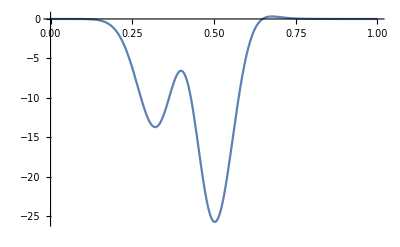

```mathematica
Plot[ω1 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] (ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2]-ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2]-(y-x/ω1) (ϕ2'[x/ω1] ϕ4'[(x-ω1+ω2)/ω2])))/.{y->0.8},{x,0,1}]
```

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];Plot3D[(ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2])))/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,1},AxesLabel->Automatic,PlotRange->All]]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics3D-

```mathematica
(ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))/.{x->1-10^-14,y->0}
```

Indeterminate

```mathematica
(ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2])))/.{x->0.5,y->0.5}
```

0.

```mathematica
(%1//.y->(ω1-(1-x) ω2)/ω1)//Expand
```

ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]-ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]

```mathematica
Quit
```

```mathematica
F[y_]=ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2];
```

```mathematica
F'[x/ω1]
```

ϕ4[((-1+x/ω1) ω1+ω2)/ω2] ϕ2'[x/ω1]+(ω1 ϕ2[x/ω1] ϕ4'[((-1+x/ω1) ω1+ω2)/ω2])/ω2

```mathematica
%//.y->(ω1-(1-x) ω2)/ω1//Simplify
```

((ω1-ω2) (ϕ3[ω1+(-1+x) ω2] ϕ2'[1+((-1+x) ω2)/ω1]+ω1 ϕ2[1+((-1+x) ω2)/ω1] ϕ3'[ω1+(-1+x) ω2]))/ω1

```mathematica
Limit[(ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))/(y-(ω1-(1-x) ω2)/ω1)^2,{x->1,y->0.5}]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

$Aborted

```mathematica
NIntegrate[(ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2](*-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2])*))/(y-(ω1-(1-x) ω2)/ω1)^2,{x,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.750003,0.922062}. NIntegrate obtained 27.45 and 52.065 for the integral and error estimates.

27.45

```mathematica
%//Simplify
```

$Aborted

```mathematica
ϕ1=ϕ2;
```

```mathematica
Clear@ϕ1
```

```mathematica
ϕ1[x_]=2.006610980894125 (*Boole[0<x<1] *)(0.3435260372885459 (1-x)^1.062071951873729 x^0.9379280481262711+0.3465843388067958 (1-x)^0.9379280481262711 x^1.062071951873729-0.8415685309096721 Sin[π x]+0.00004242901380469312 Sin[2 π x]+0.23008252047213912 Sin[3 π x]+9.867806057826455*^-6 Sin[4 π x]-0.026330516027739722 Sin[5 π x]+4.643734965851781*^-6 Sin[6 π x]+0.0005489511961456051 Sin[7 π x]+3.680614062405476*^-6 Sin[8 π x]);
```

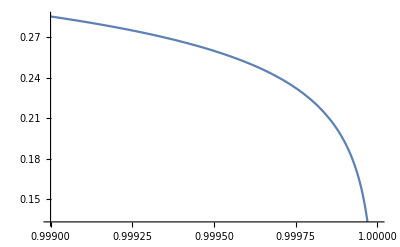

```mathematica
Plot[ϕ1'[x],{x,1-0.001,1}]
```

```mathematica
?ϕ1
```

Global`ϕ1

ϕ1=ϕn[0][ΦB]
 
ϕ1[x_]=2.00661 (0.343526 (1-x)^1.06207 x^0.937928+0.346584 (1-x)^0.937928 x^1.06207-0.841569 Sin[π x]+0.000042429 Sin[2 π x]+0.230083 Sin[3 π x]+9.86781×10^-6 Sin[4 π x]-0.0263305 Sin[5 π x]+4.64373×10^-6 Sin[6 π x]+0.000548951 Sin[7 π x]+3.68061×10^-6 Sin[8 π x])

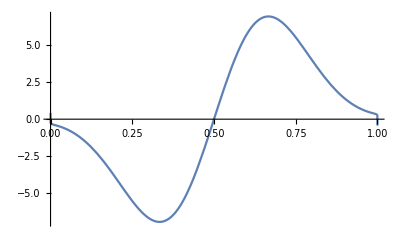

```mathematica
Plot[ϕ1'[x],{x,0,1}]
```

```mathematica
Table[ϕ1'[10^-i],{i,1,10}]
```

{-1.39576,-0.379082,-0.287859,-0.196612,-0.0759039,0.0789745,0.271424,0.505408,0.785716,1.11809}

```mathematica
Limit[Boole[0<x<1]ϕ1'[x],x->0]
```

Indeterminate

```mathematica
ϕ1'[x]
```

2.00661 ((0.322203 (1-x)^1.06207)/x^0.062072+0.368098 (1-x)^0.937928 x^0.062072-0.364849 (1-x)^0.062072 x^0.937928-(0.325071 x^1.06207)/(1-x)^0.062072-2.64387 Cos[π x]+0.000266589 Cos[2 π x]+2.16848 Cos[3 π x]+0.000124003 Cos[4 π x]-0.413599 Cos[5 π x]+0.0000875323 Cos[6 π x]+0.0120721 Cos[7 π x]+0.0000925039 Cos[8 π x])

```mathematica
Limit[ϕp1[x],x->0]
```

Indeterminate

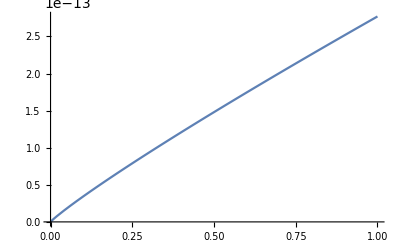

```mathematica
Plot[ϕ1[x],{x,0,0.0000000000001}]
```